```mathematica
InitialAngle=45Degree
```

45 °

```mathematica
InitialSpeed=100.0
```

100.

```mathematica
Gravity=-9.81
```

-9.81

```mathematica
InitialVelocityX=InitialSpeed*Cos[InitialAngle]
```

70.7107

```mathematica
InitialVelocityY=InitialSpeed*Sin[InitialAngle]
```

70.7107

```mathematica
ProjectileX[t_]:=InitialVelocityX*t
```

```mathematica
ProjectileY[t_]:=InitialVelocityY*t+(0.5)*Gravity*t^2
```

```mathematica
MaxTime=15
```

15

Below is a graph of the true path of the projectile.

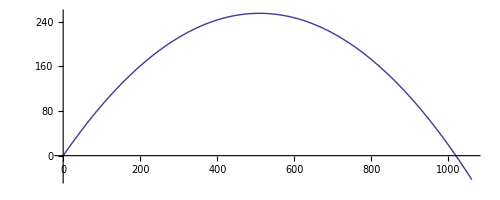

```mathematica
ParametricPlot[{ProjectileX[t], ProjectileY[t]},{t,0,MaxTime}]
```

```mathematica
NoiseLevel=10.0
```

10.

```mathematica
NoisyProjectileX[t_]:=RandomVariate[NormalDistribution[ProjectileX[t],NoiseLevel]]
```

```mathematica
NoisyProjectileY[t_]:=RandomVariate[NormalDistribution[ProjectileY[t],NoiseLevel]]
```

Assuming no friction, etc., Newton’s laws of motion state that the X-velocity will be constant, while the Y-velocity will be affected by gravity. These will become the “control updates” input into the Kalman filter.

```mathematica
VelocityX[t_]:=ProjectileX'[t]
```

```mathematica
VelocityY[t_]:=ProjectileY'[t]
```

```mathematica
NoisyVelocityX[t_]:=RandomVariate[NormalDistribution[VelocityX[t],NoiseLevel]]
```

```mathematica
NoisyVelocityY[t_]:=RandomVariate[NormalDistribution[VelocityY[t],NoiseLevel]]
```

```mathematica
InitalVelocity={InitialVelocityX,InitialVelocityY}
```

{70.7107,70.7107}

```mathematica
InitialAcceleration={0,0}
```

{0,0}

Δt represents our timestep.

```mathematica
Δt=0.1
```

0.1

A is the state transition matrix. Multiply the previous state by A to obtain the new state. (Note: ExampleA is displayed in “hold” form to preserve variables; the value A is actually evaluated.)

```mathematica
ExampleA={{1, HoldForm[Δt], 0, 0}, {0, 1, 0, 0}, {0, 0, 1, HoldForm[Δt]}, {0, 0, 0, 1}}
```

{{1,Δt,0,0},{0,1,0,0},{0,0,1,Δt},{0,0,0,1}}

```mathematica
A=ReleaseHold[ExampleA]
```

{{1,0.1,0,0},{0,1,0,0},{0,0,1,0.1},{0,0,0,1}}

B is the control matrix. Multiply any control factors by B. Note that only the third (y-position) and fourth rows (y-velocity) will have control values.

```mathematica
B={{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}}
```

{{0,0,0,0},{0,0,0,0},{0,0,1,0},{0,0,0,1}}

Note that multiplying A by the state vector and adding B multiplied by the control vector gives us the kinematic equations:

```mathematica
ExampleState=Transpose[{{X_,VelocityX_,Y_,VelocityY_}}]
```

{{X_},{VelocityX_},{Y_},{VelocityY_}}

```mathematica
ExampleControl=Transpose[{{0, 0, HoldForm[(0.5)*Gravity*Δt^2],HoldForm[Gravity*Δt]}}]
```

{{0},{0},{0.5 Gravity Δt^2},{Gravity Δt}}

(Note: ExampleControl is displayed in “hold” form whereas ControlVector is evaluated because it needs to be used later on.)

```mathematica
ControlVector=ReleaseHold[ExampleControl]
```

{{0},{0},{-0.04905},{-0.981}}

```mathematica
ExampleA.ExampleState+B.ExampleControl//MatrixForm
```

(Δt VelocityX_+X_
VelocityX_
0.5 Gravity Δt^2+Δt VelocityY_+Y_
Gravity Δt+VelocityY_)

H is the observation matrix. Multiply an incoming observation by H to obtain a state. In this case, we don’t modify the observations beforehand.

```mathematica
H=IdentityMatrix[4]
```

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

Q is the process covariance; assume no process error.

```mathematica
Q=ConstantArray[0, {4,4}]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

R is the measurement covariance; also very small.

```mathematica
R=IdentityMatrix[4]*0.2
```

{{0.2,0.,0.,0.},{0.,0.2,0.,0.},{0.,0.,0.2,0.},{0.,0.,0.,0.2}}

X0 is the initial prediction for the state; we will set it to a vastly incorrect value (initially at (0, 500) and wrong speed).

```mathematica
Wrongness=2.0
```

2.

```mathematica
X0=Transpose[{{0, Wrongness*InitialVelocityX,500,Wrongness*InitialVelocityY}}]
```

{{0},{141.421},{500},{141.421}}

P0 is the initial prediction for the covariance.

```mathematica
P0=IdentityMatrix[4]
```

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
KalmanStep[A_,B_,H_,Q_,R_,{X_,P_},NewMeasurement_,NewControl_]:=(
(* Prediction step. *)
predictedStateEstimate=A.X + B.NewControl;
predictedProbEstimate = (A.P).Transpose[A]+Q;
(* Observation step. *)
innovation = NewMeasurement-H.predictedStateEstimate;
innovationCovariance = (H.predictedProbEstimate).Transpose[H]+R;
(* Update step. *)
kalmanGain = (predictedProbEstimate.Transpose[H]).Inverse[innovationCovariance];
newStateEstimate=predictedStateEstimate+kalmanGain.innovation;
size=First[Dimensions[P]];
newProbEstimate=(IdentityMatrix[size]-kalmanGain.H).predictedProbEstimate;
{newStateEstimate,newProbEstimate}
)
```

```mathematica
KalmanProjectileMapping[OldStateProb_,NewMeasurement_]:=KalmanStep[A,B,H,Q,R,OldStateProb,NewMeasurement,ControlVector]
```

The input to the Kalman filter consists of the X-pos, X-vel, Y-pos, and Y-vel. We simulate that all measurements have noise.

```mathematica
NoisySamples=Map[(Transpose[{{NoisyProjectileX[#],NoisyVelocityX[#],NoisyProjectileY[#],NoisyVelocityY[#]}}])&,Range[0,MaxTime,Δt]]
```

{{{-0.977264},{50.9241},{-9.11508},{58.9791}},{{20.5483},{76.2826},{4.06192},{51.4879}},{{19.4754},{71.7826},{23.1824},{61.9954}},{{22.6171},{59.0253},{27.6326},{62.8807}},{{24.9715},{66.0935},{44.2694},{64.5534}},{{45.0272},{66.7029},{56.3727},{70.4025}},{{44.8576},{64.5769},{55.423},{80.767}},{{43.7472},{70.7476},{53.1936},{80.8279}},{{37.9879},{66.2931},{53.0851},{48.743}},{{70.4842},{70.6018},{64.5438},{56.6163}},{{62.492},{87.4598},{57.9371},{63.8609}},{{86.5076},{77.2782},{66.7022},{56.0272}},{{76.4873},{70.0506},{68.9304},{67.1257}},{{85.8936},{68.9451},{81.0446},{51.6056}},{{108.266},{69.5814},{105.584},{49.5557}},{{128.045},{76.2487},{90.1934},{64.528}},{{101.433},{74.4362},{85.3327},{51.2796}},{{115.677},{58.1926},{90.1912},{76.8264}},{{122.808},{67.2039},{106.468},{49.5656}},{{147.1},{67.1456},{113.976},{52.4632}},{{132.642},{86.4072},{117.838},{43.5543}},{{149.798},{72.0884},{113.634},{59.1299}},{{156.774},{74.1168},{145.373},{49.0842}},{{175.484},{58.7344},{136.96},{59.4616}},{{181.157},{74.6475},{149.114},{35.3712}},{{181.943},{73.7127},{155.926},{43.3838}},{{180.582},{76.7276},{176.961},{37.0591}},{{208.755},{84.4239},{150.554},{69.7453}},{{195.305},{50.9974},{158.229},{30.3809}},{{215.318},{69.5659},{153.471},{40.4119}},{{200.658},{81.8658},{181.271},{37.4473}},{{212.065},{78.6379},{173.345},{32.0978}},{{225.29},{80.7803},{179.61},{31.2881}},{{234.907},{71.7231},{184.309},{42.1049}},{{244.294},{77.9122},{190.576},{36.9435}},{{253.861},{74.8283},{181.787},{47.2985}},{{251.005},{65.4876},{187.57},{44.2415}},{{254.788},{71.6169},{207.737},{22.1323}},{{259.372},{85.7392},{189.986},{22.7391}},{{272.605},{69.4347},{195.019},{21.9634}},{{286.298},{64.9812},{206.893},{15.7669}},{{291.893},{63.0069},{198.667},{17.7304}},{{316.136},{69.1303},{200.926},{27.6029}},{{293.378},{72.6905},{217.432},{28.9118}},{{311.07},{64.273},{215.797},{28.9027}},{{328.648},{54.9567},{218.133},{19.6681}},{{332.772},{55.7261},{228.268},{11.2844}},{{326.019},{58.6247},{238.985},{15.2097}},{{335.541},{75.2291},{231.372},{26.6853}},{{337.203},{93.9433},{241.137},{22.2423}},{{353.593},{73.0799},{210.193},{-5.4543}},{{362.101},{58.6355},{222.451},{8.51478}},{{379.583},{63.4711},{234.199},{7.97834}},{{371.682},{52.9553},{230.803},{5.09152}},{{387.091},{92.7772},{245.343},{28.8778}},{{385.04},{65.7829},{234.859},{-0.858278}},{{416.617},{83.3759},{255.908},{18.7782}},{{417.115},{90.3896},{256.042},{43.2543}},{{419.985},{74.5619},{247.347},{13.9683}},{{418.655},{68.3453},{268.626},{17.3228}},{{429.943},{91.9274},{251.641},{4.03354}},{{418.635},{76.3551},{264.76},{2.19909}},{{445.565},{71.4139},{256.263},{-4.96252}},{{458.868},{66.6527},{237.353},{-1.64407}},{{457.853},{83.2962},{258.548},{16.7165}},{{451.974},{68.7787},{250.229},{15.6273}},{{477.41},{82.5885},{256.031},{-9.43709}},{{461.654},{73.5155},{242.523},{2.05946}},{{485.926},{65.5118},{248.548},{-8.02326}},{{471.968},{85.4093},{260.762},{-13.8397}},{{511.174},{66.0791},{251.559},{12.0148}},{{517.363},{71.511},{272.363},{-0.79852}},{{488.52},{78.7329},{261.632},{4.33803}},{{512.564},{71.9427},{263.599},{5.96112}},{{528.969},{61.6819},{259.255},{9.28531}},{{528.172},{73.2542},{257.131},{-2.9135}},{{531.715},{74.5378},{258.815},{1.3937}},{{543.638},{66.2013},{243.479},{7.54361}},{{545.097},{81.1885},{248.162},{-0.996954}},{{540.786},{63.1853},{252.378},{-20.526}},{{562.603},{73.7837},{260.619},{-3.52757}},{{580.338},{83.5461},{244.137},{-22.0118}},{{575.719},{63.1587},{243.279},{-1.24685}},{{572.375},{72.9983},{240.813},{-10.577}},{{592.278},{69.6317},{231.689},{-1.46313}},{{608.42},{61.0418},{258.911},{12.2286}},{{596.838},{73.698},{255.713},{-9.21092}},{{613.684},{68.8548},{242.426},{-13.1804}},{{599.126},{48.0531},{260.533},{-22.6512}},{{635.731},{58.501},{245.448},{-34.4459}},{{631.6},{43.6124},{237.452},{-30.5705}},{{645.448},{82.3892},{242.891},{-11.0723}},{{650.708},{80.3312},{221.474},{-22.8754}},{{660.827},{69.2279},{224.792},{-20.2902}},{{670.507},{71.2718},{222.89},{-8.37602}},{{660.307},{71.4052},{228.044},{-16.0415}},{{680.562},{77.2136},{224.396},{-14.3858}},{{696.106},{50.7859},{211.845},{-33.2518}},{{691.284},{56.1177},{203.609},{-36.8371}},{{702.338},{63.8805},{210.596},{-27.6875}},{{703.114},{85.9243},{224.526},{-30.2511}},{{716.735},{73.0089},{213.369},{-36.9918}},{{714.087},{74.5509},{209.407},{-12.845}},{{731.782},{80.9246},{213.657},{-31.258}},{{716.275},{46.5472},{218.146},{-37.9658}},{{746.397},{95.9528},{185.351},{-20.681}},{{755.372},{67.6176},{204.75},{-27.4321}},{{768.},{77.9278},{197.406},{-41.7355}},{{773.77},{77.2102},{201.616},{-18.1501}},{{761.83},{63.6715},{187.783},{-30.6379}},{{772.627},{53.9818},{190.977},{-23.1546}},{{786.318},{95.5232},{172.104},{-36.3786}},{{779.727},{68.4854},{171.388},{-18.9606}},{{802.601},{57.581},{165.43},{-46.1258}},{{791.664},{69.9212},{146.704},{-37.3697}},{{818.883},{76.4692},{172.249},{-40.5876}},{{812.857},{72.453},{170.959},{-31.7406}},{{839.797},{68.7389},{140.771},{-45.0553}},{{849.449},{83.9162},{167.376},{-39.1322}},{{870.163},{67.3376},{142.622},{-36.1902}},{{851.345},{72.8608},{150.604},{-50.3194}},{{841.046},{71.2506},{126.865},{-64.2777}},{{875.738},{80.7659},{127.111},{-49.5614}},{{865.974},{83.2545},{130.227},{-57.5381}},{{870.98},{63.8625},{130.496},{-54.7133}},{{892.345},{79.2604},{131.246},{-39.1068}},{{890.587},{45.1268},{118.414},{-49.3385}},{{898.216},{66.1666},{106.854},{-58.4831}},{{912.691},{80.6891},{105.257},{-61.4657}},{{908.985},{61.3349},{95.8484},{-72.9053}},{{921.178},{72.879},{105.737},{-42.1222}},{{925.635},{67.6255},{92.8052},{-47.8782}},{{930.963},{71.7604},{80.0416},{-58.7469}},{{960.125},{74.7233},{76.3803},{-54.3141}},{{955.387},{65.9332},{61.0367},{-42.4562}},{{970.829},{70.1384},{52.6337},{-59.4589}},{{971.527},{71.6648},{56.9958},{-53.9446}},{{980.861},{66.8592},{30.7697},{-62.1512}},{{973.694},{78.2977},{40.1372},{-69.3443}},{{987.482},{85.9182},{46.1222},{-61.4606}},{{975.633},{70.5384},{8.80376},{-63.7206}},{{1020.59},{71.8719},{28.9849},{-81.4564}},{{1005.4},{58.9374},{10.6449},{-64.5187}},{{1015.33},{83.8887},{9.79139},{-78.2027}},{{1019.18},{83.5326},{1.76295},{-82.7435}},{{1011.26},{76.2706},{-2.88778},{-61.8427}},{{1042.79},{87.9002},{-26.1143},{-77.3746}},{{1037.81},{61.4627},{-24.6878},{-74.4192}},{{1052.1},{61.484},{-36.8617},{-64.6155}},{{1068.71},{61.3599},{-50.6838},{-66.1172}},{{1047.15},{68.0328},{-43.8163},{-91.6825}}}

```mathematica
KalmanData=FoldList[KalmanProjectileMapping,{X0,P0},NoisySamples]
```

{{{{0},{141.421},{500},{141.421}},{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}},{{{0.283978},{65.9019},{76.8355},{65.3935}},{{0.166713,0.00277393,0.,0.},{0.00277393,0.166436,0.,0.},{0.,0.,0.166713,0.00277393},{0.,0.,0.00277393,0.166436}}},{{{13.4138},{70.9948},{46.7791},{56.2785}},{{0.0912757,0.00576132,0.,0.},{0.00576132,0.090535,0.,0.},{0.,0.,0.0912757,0.00576132},{0.,0.,0.00576132,0.090535}}},{{{20.2123},{71.2027},{43.3597},{56.3558}},{{0.0632843,0.00697134,0.,0.},{0.00697134,0.0619675,0.,0.},{0.,0.,0.0632843,0.00697134},{0.,0.,0.00697134,0.0619675}}},{{{25.7183},{68.1663},{44.0256},{56.3263}},{{0.0488492,0.00759777,0.,0.},{0.00759777,0.0469274,0.,0.},{0.,0.,0.0488492,0.00759777},{0.,0.,0.00759777,0.0469274}}},{{{30.9343},{67.4756},{48.9037},{56.8646}},{{0.0401447,0.0079566,0.,0.},{0.0079566,0.037613,0.,0.},{0.,0.,0.0401447,0.0079566},{0.,0.,0.0079566,0.037613}}},{{{38.9134},{67.6548},{55.4489},{58.2274}},{{0.034392,0.00816697,0.,0.},{0.00816697,0.0312563,0.,0.},{0.,0.,0.034392,0.00816697},{0.,0.,0.00816697,0.0312563}}},{{{45.4267},{67.211},{61.3166},{60.1376}},{{0.030355,0.00828402,0.,0.},{0.00828402,0.0266272,0.,0.},{0.,0.,0.030355,0.00828402},{0.,0.,0.00828402,0.0266272}}},{{{51.1444},{67.2692},{66.2547},{61.072}},{{0.0273997,0.00833709,0.,0.},{0.00833709,0.023096,0.,0.},{0.,0.,0.0273997,0.00833709},{0.,0.,0.00833709,0.023096}}},{{{55.3285},{66.3406},{69.4199},{58.1366}},{{0.0251672,0.00834345,0.,0.},{0.00834345,0.0203068,0.,0.},{0.,0.,0.0251672,0.00834345},{0.,0.,0.00834345,0.0203068}}},{{{63.1384},{67.0793},{73.9151},{56.6646}},{{0.0234389,0.00831417,0.,0.},{0.00831417,0.0180435,0.,0.},{0.,0.,0.0234389,0.00831417},{0.,0.,0.00831417,0.0180435}}},{{{69.876},{68.4232},{77.4866},{55.4531}},{{0.022074,0.00825683,0.,0.},{0.00825683,0.0161672,0.,0.},{0.,0.,0.022074,0.00825683},{0.,0.,0.00825683,0.0161672}}},{{{78.1072},{69.4691},{81.3388},{53.9199}},{{0.0209779,0.00817693,0.,0.},{0.00817693,0.0145846,0.,0.},{0.,0.,0.0209779,0.00817693},{0.,0.,0.00817693,0.0145846}}},{{{84.2173},{69.1616},{85.4721},{53.1604}},{{0.0200844,0.00807866,0.,0.},{0.00807866,0.0132306,0.,0.},{0.,0.,0.0200844,0.00807866},{0.,0.,0.00807866,0.0132306}}},{{{90.618},{68.9398},{89.7785},{51.7587}},{{0.0193461,0.00796535,0.,0.},{0.00796535,0.0120584,0.,0.},{0.,0.,0.0193461,0.00796535},{0.,0.,0.00796535,0.0120584}}},{{{98.5441},{69.3968},{95.8574},{51.1288}},{{0.0187282,0.00783972,0.,0.},{0.00783972,0.0110337,0.,0.},{0.,0.,0.0187282,0.00783972},{0.,0.,0.00783972,0.0110337}}},{{{107.801},{70.6129},{100.499},{50.463}},{{0.0182046,0.00770404,0.,0.},{0.00770404,0.0101303,0.,0.},{0.,0.,0.0182046,0.00770404},{0.,0.,0.00770404,0.0101303}}},{{{113.815},{70.2835},{103.774},{48.8036}},{{0.0177552,0.00756027,0.,0.},{0.00756027,0.00932831,0.,0.},{0.,0.,0.0177552,0.00756027},{0.,0.,0.00756027,0.00932831}}},{{{119.947},{69.5715},{108.081},{48.3893}},{{0.0173649,0.00741007,0.,0.},{0.00741007,0.00861196,0.,0.},{0.,0.,0.0173649,0.00741007},{0.,0.,0.00741007,0.00861196}}},{{{126.469},{69.3285},{112.404},{47.262}},{{0.0170217,0.00725492,0.,0.},{0.00725492,0.00796879,0.,0.},{0.,0.,0.0170217,0.00725492},{0.,0.,0.00725492,0.00796879}}},{{{134.47},{69.7339},{117.041},{46.3992}},{{0.016716,0.00709609,0.,0.},{0.00709609,0.00738871,0.,0.},{0.,0.,0.016716,0.00709609},{0.,0.,0.00709609,0.00738871}}},{{{141.298},{70.0009},{121.256},{45.2227}},{{0.0164406,0.00693471,0.,0.},{0.00693471,0.00686348,0.,0.},{0.,0.,0.0164406,0.00693471},{0.,0.,0.00693471,0.00686348}}},{{{148.49},{70.1184},{125.254},{44.3076}},{{0.0161895,0.00677176,0.,0.},{0.00677176,0.00638628,0.,0.},{0.,0.,0.0161895,0.00677176},{0.,0.,0.00677176,0.00638628}}},{{{155.735},{70.2794},{131.081},{44.0179}},{{0.015958,0.00660811,0.,0.},{0.00660811,0.0059514,0.,0.},{0.,0.,0.015958,0.00660811},{0.,0.,0.00660811,0.0059514}}},{{{163.392},{70.3687},{136.083},{43.5421}},{{0.0157422,0.00644451,0.,0.},{0.00644451,0.00555403,0.,0.},{0.,0.,0.0157422,0.00644451},{0.,0.,0.00644451,0.00555403}}},{{{171.397},{70.8167},{140.841},{42.6486}},{{0.0155392,0.0062816,0.,0.},{0.0062816,0.00519004,0.,0.},{0.,0.,0.0155392,0.0062816},{0.,0.,0.0062816,0.00519004}}},{{{178.833},{70.993},{145.943},{42.0419}},{{0.0153466,0.00611996,0.,0.},{0.00611996,0.00485593,0.,0.},{0.,0.,0.0153466,0.00611996},{0.,0.,0.00611996,0.00485593}}},{{{185.698},{70.964},{152.016},{41.7704}},{{0.0151624,0.00596007,0.,0.},{0.00596007,0.00454865,0.,0.},{0.,0.,0.0151624,0.00596007},{0.,0.,0.00596007,0.00454865}}},{{{194.381},{71.7141},{156.565},{41.2448}},{{0.014985,0.00580233,0.,0.},{0.00580233,0.00426553,0.,0.},{0.,0.,0.014985,0.00580233},{0.,0.,0.00580233,0.00426553}}},{{{200.504},{71.1229},{160.183},{39.9978}},{{0.0148133,0.00564709,0.,0.},{0.00564709,0.00400425,0.,0.},{0.,0.,0.0148133,0.00564709},{0.,0.,0.00564709,0.00400425}}},{{{208.138},{71.3052},{163.391},{38.7502}},{{0.0146462,0.00549464,0.,0.},{0.00549464,0.00376277,0.,0.},{0.,0.,0.0146462,0.00549464},{0.,0.,0.00549464,0.00376277}}},{{{214.493},{71.1016},{168.226},{38.1391}},{{0.0144829,0.00534522,0.,0.},{0.00534522,0.00353928,0.,0.},{0.,0.,0.0144829,0.00534522},{0.,0.,0.00534522,0.00353928}}},{{{221.116},{70.9792},{171.956},{37.109}},{{0.0143229,0.005199,0.,0.},{0.005199,0.00333216,0.,0.},{0.,0.,0.0143229,0.005199},{0.,0.,0.005199,0.00333216}}},{{{228.254},{71.0592},{175.778},{36.1529}},{{0.0141657,0.00505614,0.,0.},{0.00505614,0.00313999,0.,0.},{0.,0.,0.0141657,0.00505614},{0.,0.,0.00505614,0.00313999}}},{{{235.345},{71.0579},{179.863},{35.3966}},{{0.0140109,0.00491674,0.,0.},{0.00491674,0.00296147,0.,0.},{0.,0.,0.0140109,0.00491674},{0.,0.,0.00491674,0.00296147}}},{{{242.742},{71.1978},{183.914},{34.6236}},{{0.0138582,0.00478089,0.,0.},{0.00478089,0.00279547,0.,0.},{0.,0.,0.0138582,0.00478089},{0.,0.,0.00478089,0.00279547}}},{{{250.22},{71.3386},{187.265},{33.6941}},{{0.0137075,0.00464863,0.,0.},{0.00464863,0.00264094,0.,0.},{0.,0.,0.0137075,0.00464863},{0.,0.,0.00464863,0.00264094}}},{{{256.792},{71.1221},{190.642},{32.7889}},{{0.0135585,0.00451999,0.,0.},{0.00451999,0.00249694,0.,0.},{0.,0.,0.0135585,0.00451999},{0.,0.,0.00451999,0.00249694}}},{{{263.303},{70.9276},{194.589},{31.9983}},{{0.0134112,0.00439498,0.,0.},{0.00439498,0.00236263,0.,0.},{0.,0.,0.0134112,0.00439498},{0.,0.,0.00439498,0.00236263}}},{{{269.982},{70.8578},{197.048},{30.759}},{{0.0132655,0.00427358,0.,0.},{0.00427358,0.00223724,0.,0.},{0.,0.,0.0132655,0.00427358},{0.,0.,0.00427358,0.00223724}}},{{{276.745},{70.75},{199.581},{29.5901}},{{0.0131213,0.00415577,0.,0.},{0.00415577,0.00212007,0.,0.},{0.,0.,0.0131213,0.00415577},{0.,0.,0.00415577,0.00212007}}},{{{283.864},{70.742},{202.517},{28.569}},{{0.0129786,0.0040415,0.,0.},{0.0040415,0.0020105,0.,0.},{0.,0.,0.0129786,0.0040415},{0.,0.,0.0040415,0.0020105}}},{{{290.848},{70.687},{204.704},{27.3631}},{{0.0128374,0.00393072,0.,0.},{0.00393072,0.00190794,0.,0.},{0.,0.,0.0128374,0.00393072},{0.,0.,0.00393072,0.00190794}}},{{{299.043},{71.0212},{207.004},{26.2696}},{{0.0126976,0.00382337,0.,0.},{0.00382337,0.00181186,0.,0.},{0.,0.,0.0126976,0.00382337},{0.,0.,0.00382337,0.00181186}}},{{{305.375},{70.7981},{210.142},{25.4657}},{{0.0125594,0.00371939,0.,0.},{0.00371939,0.00172179,0.,0.},{0.,0.,0.0125594,0.00371939},{0.,0.,0.00371939,0.00172179}}},{{{312.25},{70.7197},{212.916},{24.578}},{{0.0124227,0.00361869,0.,0.},{0.00361869,0.00163729,0.,0.},{0.,0.,0.0124227,0.00361869},{0.,0.,0.00361869,0.00163729}}},{{{319.618},{70.7611},{215.428},{23.6159}},{{0.0122876,0.00352121,0.,0.},{0.00352121,0.00155794,0.,0.},{0.,0.,0.0122876,0.00352121},{0.,0.,0.00352121,0.00155794}}},{{{326.806},{70.7537},{218.186},{22.7311}},{{0.0121539,0.00342686,0.,0.},{0.00342686,0.00148338,0.,0.},{0.,0.,0.0121539,0.00342686},{0.,0.,0.00342686,0.00148338}}},{{{333.206},{70.5369},{221.417},{22.0136}},{{0.0120218,0.00333556,0.,0.},{0.00333556,0.00141327,0.,0.},{0.,0.,0.0120218,0.00333556},{0.,0.,0.00333556,0.00141327}}},{{{340.055},{70.4919},{224.125},{21.1974}},{{0.0118914,0.00324721,0.,0.},{0.00324721,0.0013473,0.,0.},{0.,0.,0.0118914,0.00324721},{0.,0.,0.00324721,0.0013473}}},{{{346.893},{70.486},{227.107},{20.4656}},{{0.0117625,0.00316175,0.,0.},{0.00316175,0.00128518,0.,0.},{0.,0.,0.0117625,0.00316175},{0.,0.,0.00316175,0.00128518}}},{{{353.961},{70.4966},{227.62},{19.0405}},{{0.0116352,0.00307906,0.,0.},{0.00307906,0.00122664,0.,0.},{0.,0.,0.0116352,0.00307906},{0.,0.,0.00307906,0.00122664}}},{{{360.896},{70.4434},{228.928},{17.8983}},{{0.0115095,0.00299908,0.,0.},{0.00299908,0.00117145,0.,0.},{0.,0.,0.0115095,0.00299908},{0.,0.,0.00299908,0.00117145}}},{{{368.501},{70.5745},{230.739},{16.9188}},{{0.0113855,0.00292171,0.,0.},{0.00292171,0.00111937,0.,0.},{0.,0.,0.0113855,0.00292171},{0.,0.,0.00292171,0.00111937}}},{{{375.089},{70.425},{232.139},{15.8573}},{{0.0112631,0.00284688,0.,0.},{0.00284688,0.00107019,0.,0.},{0.,0.,0.0112631,0.00284688},{0.,0.,0.00284688,0.00107019}}},{{{382.718},{70.6082},{234.519},{15.1098}},{{0.0111424,0.00277448,0.,0.},{0.00277448,0.00102374,0.,0.},{0.,0.,0.0111424,0.00277448},{0.,0.,0.00277448,0.00102374}}},{{{389.453},{70.5205},{235.717},{14.0402}},{{0.0110234,0.00270445,0.,0.},{0.00270445,0.000979822,0.,0.},{0.,0.,0.0110234,0.00270445},{0.,0.,0.00270445,0.000979822}}},{{{397.771},{70.846},{238.174},{13.3344}},{{0.010906,0.0026367,0.,0.},{0.0026367,0.000938279,0.,0.},{0.,0.,0.010906,0.0026367},{0.,0.,0.0026367,0.000938279}}},{{{405.768},{71.0914},{240.751},{12.7055}},{{0.0107903,0.00257115,0.,0.},{0.00257115,0.000898959,0.,0.},{0.,0.,0.0107903,0.00257115},{0.,0.,0.00257115,0.000898959}}},{{{413.3},{71.1955},{242.287},{11.8015}},{{0.0106762,0.00250772,0.,0.},{0.00250772,0.00086172,0.,0.},{0.,0.,0.0106762,0.00250772},{0.,0.,0.00250772,0.00086172}}},{{{420.292},{71.1621},{244.829},{11.1557}},{{0.0105638,0.00244635,0.,0.},{0.00244635,0.000826432,0.,0.},{0.,0.,0.0105638,0.00244635},{0.,0.,0.00244635,0.000826432}}},{{{427.788},{71.2747},{246.123},{10.2189}},{{0.010453,0.00238695,0.,0.},{0.00238695,0.000792972,0.,0.},{0.,0.,0.010453,0.00238695},{0.,0.,0.00238695,0.000792972}}},{{{434.133},{71.1044},{247.927},{9.41688}},{{0.0103439,0.00232946,0.,0.},{0.00232946,0.000761229,0.,0.},{0.,0.,0.0103439,0.00232946},{0.,0.,0.00232946,0.000761229}}},{{{441.468},{71.1547},{249.049},{8.47152}},{{0.0102364,0.0022738,0.,0.},{0.0022738,0.000731097,0.,0.},{0.,0.,0.0102364,0.0022738},{0.,0.,0.0022738,0.000731097}}},{{{449.055},{71.253},{249.112},{7.31977}},{{0.0101305,0.00221992,0.,0.},{0.00221992,0.000702479,0.,0.},{0.,0.,0.0101305,0.00221992},{0.,0.,0.00221992,0.000702479}}},{{{456.394},{71.3118},{250.347},{6.46868}},{{0.0100262,0.00216775,0.,0.},{0.00216775,0.000675285,0.,0.},{0.,0.,0.0100262,0.00216775},{0.,0.,0.00216775,0.000675285}}},{{{462.925},{71.1813},{251.016},{5.51302}},{{0.00992353,0.00211722,0.,0.},{0.00211722,0.000649429,0.,0.},{0.,0.,0.00992353,0.00211722},{0.,0.,0.00211722,0.000649429}}},{{{470.523},{71.2931},{251.596},{4.53505}},{{0.00982242,0.00206827,0.,0.},{0.00206827,0.000624834,0.,0.},{0.,0.,0.00982242,0.00206827},{0.,0.,0.00206827,0.000624834}}},{{{476.897},{71.1382},{251.524},{3.45379}},{{0.00972287,0.00202086,0.,0.},{0.00202086,0.000601425,0.,0.},{0.,0.,0.00972287,0.00202086},{0.,0.,0.00202086,0.000601425}}},{{{484.048},{71.1408},{251.56},{2.41008}},{{0.00962486,0.00197492,0.,0.},{0.00197492,0.000579135,0.,0.},{0.,0.,0.00962486,0.00197492},{0.,0.,0.00197492,0.000579135}}},{{{490.385},{70.9953},{252.033},{1.47346}},{{0.00952838,0.00193039,0.,0.},{0.00193039,0.000557898,0.,0.},{0.,0.,0.00952838,0.00193039},{0.,0.,0.00193039,0.000557898}}},{{{498.084},{71.1113},{252.213},{0.51804}},{{0.00943339,0.00188723,0.,0.},{0.00188723,0.000537656,0.,0.},{0.,0.,0.00943339,0.00188723},{0.,0.,0.00188723,0.000537656}}},{{{505.767},{71.2246},{253.154},{-0.277933}},{{0.0093399,0.0018454,0.,0.},{0.0018454,0.000518353,0.,0.},{0.,0.,0.0093399,0.0018454},{0.,0.,0.0018454,0.000518353}}},{{{511.83},{71.0235},{253.523},{-1.16774}},{{0.00924786,0.00180483,0.,0.},{0.00180483,0.000499937,0.,0.},{0.,0.,0.00924786,0.00180483},{0.,0.,0.00180483,0.000499937}}},{{{518.649},{70.9695},{253.898},{-2.03878}},{{0.00915727,0.00176548,0.,0.},{0.00176548,0.000482358,0.,0.},{0.,0.,0.00915727,0.00176548},{0.,0.,0.00176548,0.000482358}}},{{{525.812},{70.9757},{254.006},{-2.94268}},{{0.0090681,0.00172732,0.,0.},{0.00172732,0.000465571,0.,0.},{0.,0.,0.0090681,0.00172732},{0.,0.,0.00172732,0.000465571}}},{{{532.716},{70.9408},{253.827},{-3.89209}},{{0.00898034,0.00169029,0.,0.},{0.00169029,0.000449532,0.,0.},{0.,0.,0.00898034,0.00169029},{0.,0.,0.00169029,0.000449532}}},{{{539.48},{70.8816},{253.681},{-4.8146}},{{0.00889395,0.00165436,0.,0.},{0.00165436,0.000434203,0.,0.},{0.,0.,0.00889395,0.00165436},{0.,0.,0.00165436,0.000434203}}},{{{546.401},{70.8481},{252.833},{-5.84593}},{{0.00880892,0.00161948,0.,0.},{0.00161948,0.000419544,0.,0.},{0.,0.,0.00880892,0.00161948},{0.,0.,0.00161948,0.000419544}}},{{{553.202},{70.8025},{252.069},{-6.84711}},{{0.00872523,0.00158563,0.,0.},{0.00158563,0.000405522,0.,0.},{0.,0.,0.00872523,0.00158563},{0.,0.,0.00158563,0.000405522}}},{{{559.381},{70.6362},{251.282},{-7.84491}},{{0.00864285,0.00155276,0.,0.},{0.00155276,0.000392101,0.,0.},{0.,0.,0.00864285,0.00155276},{0.,0.,0.00155276,0.000392101}}},{{{566.304},{70.613},{250.924},{-8.73853}},{{0.00856177,0.00152084,0.,0.},{0.00152084,0.000379252,0.,0.},{0.,0.,0.00856177,0.00152084},{0.,0.,0.00152084,0.000379252}}},{{{573.757},{70.6886},{249.661},{-9.78576}},{{0.00848195,0.00148983,0.,0.},{0.00148983,0.000366945,0.,0.},{0.,0.,0.00848195,0.00148983},{0.,0.,0.00148983,0.000366945}}},{{{580.556},{70.638},{248.478},{-10.7889}},{{0.00840339,0.00145971,0.,0.},{0.00145971,0.000355152,0.,0.},{0.,0.,0.00840339,0.00145971},{0.,0.,0.00145971,0.000355152}}},{{{587.002},{70.533},{247.086},{-11.8146}},{{0.00832605,0.00143044,0.,0.},{0.00143044,0.000343847,0.,0.},{0.,0.,0.00832605,0.00143044},{0.,0.,0.00143044,0.000343847}}},{{{593.976},{70.5191},{245.351},{-12.8761}},{{0.00824992,0.00140199,0.,0.},{0.00140199,0.000333006,0.,0.},{0.,0.,0.00824992,0.00140199},{0.,0.,0.00140199,0.000333006}}},{{{601.265},{70.5546},{244.802},{-13.7126}},{{0.00817497,0.00137433,0.,0.},{0.00137433,0.000322606,0.,0.},{0.,0.,0.00817497,0.00137433},{0.,0.,0.00137433,0.000322606}}},{{{607.877},{70.4821},{243.919},{-14.602}},{{0.00810119,0.00134744,0.,0.},{0.00134744,0.000312625,0.,0.},{0.,0.,0.00810119,0.00134744},{0.,0.,0.00134744,0.000312625}}},{{{614.864},{70.4715},{242.426},{-15.5792}},{{0.00802855,0.0013213,0.,0.},{0.0013213,0.000303043,0.,0.},{0.,0.,0.00802855,0.0013213},{0.,0.,0.0013213,0.000303043}}},{{{620.86},{70.2909},{241.564},{-16.4415}},{{0.00795703,0.00129586,0.,0.},{0.00129586,0.000293841,0.,0.},{0.,0.,0.00795703,0.00129586},{0.,0.,0.00129586,0.000293841}}},{{{628.123},{70.3239},{239.982},{-17.4113}},{{0.00788661,0.00127112,0.,0.},{0.00127112,0.000284999,0.,0.},{0.,0.,0.00788661,0.00127112},{0.,0.,0.00127112,0.000284999}}},{{{634.85},{70.2648},{238.087},{-18.4137}},{{0.00781727,0.00124705,0.,0.},{0.00124705,0.000276502,0.,0.},{0.,0.,0.00781727,0.00124705},{0.,0.,0.00124705,0.000276502}}},{{{642.089},{70.303},{236.507},{-19.3426}},{{0.007749,0.00122362,0.,0.},{0.00122362,0.000268332,0.,0.},{0.,0.,0.007749,0.00122362},{0.,0.,0.00122362,0.000268332}}},{{{649.24},{70.3256},{234.007},{-20.4053}},{{0.00768177,0.00120081,0.,0.},{0.00120081,0.000260475,0.,0.},{0.,0.,0.00768177,0.00120081},{0.,0.,0.00120081,0.000260475}}},{{{656.44},{70.351},{231.653},{-21.4269}},{{0.00761555,0.00117861,0.,0.},{0.00117861,0.000252916,0.,0.},{0.,0.,0.00761555,0.00117861},{0.,0.,0.00117861,0.000252916}}},{{{663.746},{70.3928},{229.294},{-22.4287}},{{0.00755035,0.00115699,0.,0.},{0.00115699,0.00024564,0.,0.},{0.,0.,0.00755035,0.00115699},{0.,0.,0.00115699,0.00024564}}},{{{670.399},{70.3345},{227.083},{-23.3949}},{{0.00748612,0.00113593,0.,0.},{0.00113593,0.000238637,0.,0.},{0.,0.,0.00748612,0.00113593},{0.,0.,0.00113593,0.000238637}}},{{{677.587},{70.3599},{224.739},{-24.366}},{{0.00742286,0.00111542,0.,0.},{0.00111542,0.000231892,0.,0.},{0.,0.,0.00742286,0.00111542},{0.,0.,0.00111542,0.000231892}}},{{{684.938},{70.4008},{221.827},{-25.4129}},{{0.00736055,0.00109543,0.,0.},{0.00109543,0.000225394,0.,0.},{0.,0.,0.00736055,0.00109543},{0.,0.,0.00109543,0.000225394}}},{{{691.876},{70.3814},{218.61},{-26.4895}},{{0.00729917,0.00107596,0.,0.},{0.00107596,0.000219132,0.,0.},{0.,0.,0.00729917,0.00107596},{0.,0.,0.00107596,0.000219132}}},{{{699.004},{70.3926},{215.719},{-27.4988}},{{0.0072387,0.00105698,0.,0.},{0.00105698,0.000213097,0.,0.},{0.,0.,0.0072387,0.00105698},{0.,0.,0.00105698,0.000213097}}},{{{706.018},{70.3935},{213.327},{-28.4214}},{{0.00717913,0.00103847,0.,0.},{0.00103847,0.000207277,0.,0.},{0.,0.,0.00717913,0.00103847},{0.,0.,0.00103847,0.000207277}}},{{{713.202},{70.4149},{210.502},{-29.395}},{{0.00712043,0.00102044,0.,0.},{0.00102044,0.000201664,0.,0.},{0.,0.,0.00712043,0.00102044},{0.,0.,0.00102044,0.000201664}}},{{{720.047},{70.388},{207.668},{-30.3494}},{{0.00706259,0.00100284,0.,0.},{0.00100284,0.000196248,0.,0.},{0.,0.,0.00706259,0.00100284},{0.,0.,0.00100284,0.000196248}}},{{{727.302},{70.4212},{204.902},{-31.2856}},{{0.0070056,0.000985686,0.,0.},{0.000985686,0.000191022,0.,0.},{0.,0.,0.0070056,0.000985686},{0.,0.,0.000985686,0.000191022}}},{{{733.601},{70.3115},{202.268},{-32.1923}},{{0.00694944,0.000968949,0.,0.},{0.000968949,0.000185976,0.,0.},{0.,0.,0.00694944,0.000968949},{0.,0.,0.000968949,0.000185976}}},{{{740.953},{70.3622},{198.588},{-33.227}},{{0.00689409,0.00095262,0.,0.},{0.00095262,0.000181104,0.,0.},{0.,0.,0.00689409,0.00095262},{0.,0.,0.00095262,0.000181104}}},{{{748.229},{70.3943},{195.574},{-34.1574}},{{0.00683954,0.000936685,0.,0.},{0.000936685,0.000176398,0.,0.},{0.,0.,0.00683954,0.000936685},{0.,0.,0.000936685,0.000176398}}},{{{755.735},{70.4595},{192.259},{-35.1197}},{{0.00678577,0.000921134,0.,0.},{0.000921134,0.000171851,0.,0.},{0.,0.,0.00678577,0.000921134},{0.,0.,0.000921134,0.000171851}}},{{{763.181},{70.5149},{189.214},{-36.0271}},{{0.00673277,0.000905953,0.,0.},{0.000905953,0.000167457,0.,0.},{0.,0.,0.00673277,0.000905953},{0.,0.,0.000905953,0.000167457}}},{{{769.921},{70.4719},{185.665},{-36.993}},{{0.00668053,0.000891132,0.,0.},{0.000891132,0.000163209,0.,0.},{0.,0.,0.00668053,0.000891132},{0.,0.,0.000891132,0.000163209}}},{{{776.752},{70.4397},{182.282},{-37.9225}},{{0.00662902,0.00087666,0.,0.},{0.00087666,0.000159101,0.,0.},{0.,0.,0.00662902,0.00087666},{0.,0.,0.00087666,0.000159101}}},{{{783.988},{70.47},{178.243},{-38.9289}},{{0.00657824,0.000862526,0.,0.},{0.000862526,0.000155129,0.,0.},{0.,0.,0.00657824,0.000862526},{0.,0.,0.000862526,0.000155129}}},{{{790.657},{70.4206},{174.295},{-39.9064}},{{0.00652817,0.000848721,0.,0.},{0.000848721,0.000151285,0.,0.},{0.,0.,0.00652817,0.000848721},{0.,0.,0.000848721,0.000151285}}},{{{797.804},{70.4316},{170.077},{-40.9114}},{{0.0064788,0.000835234,0.,0.},{0.000835234,0.000147566,0.,0.},{0.,0.,0.0064788,0.000835234},{0.,0.,0.000835234,0.000147566}}},{{{804.422},{70.377},{165.337},{-41.9682}},{{0.00643011,0.000822056,0.,0.},{0.000822056,0.000143966,0.,0.},{0.,0.,0.00643011,0.000822056},{0.,0.,0.000822056,0.000143966}}},{{{811.721},{70.4113},{161.457},{-42.9024}},{{0.0063821,0.000809179,0.,0.},{0.000809179,0.000140481,0.,0.},{0.,0.,0.0063821,0.000809179},{0.,0.,0.000809179,0.000140481}}},{{{818.583},{70.3892},{157.604},{-43.8199}},{{0.00633474,0.000796593,0.,0.},{0.000796593,0.000137106,0.,0.},{0.,0.,0.00633474,0.000796593},{0.,0.,0.000796593,0.000137106}}},{{{826.061},{70.4437},{152.782},{-44.8498}},{{0.00628804,0.000784289,0.,0.},{0.000784289,0.000133836,0.,0.},{0.,0.,0.00628804,0.000784289},{0.,0.,0.000784289,0.000133836}}},{{{833.668},{70.5156},{148.871},{-45.7525}},{{0.00624197,0.000772261,0.,0.},{0.000772261,0.000130669,0.,0.},{0.,0.,0.00624197,0.000772261},{0.,0.,0.000772261,0.000130669}}},{{{841.619},{70.6255},{144.237},{-46.733}},{{0.00619652,0.0007605,0.,0.},{0.0007605,0.000127599,0.,0.},{0.,0.,0.00619652,0.0007605},{0.,0.,0.0007605,0.000127599}}},{{{848.772},{70.6369},{139.846},{-47.6741}},{{0.00615169,0.000748997,0.,0.},{0.000748997,0.000124624,0.,0.},{0.,0.,0.00615169,0.000748997},{0.,0.,0.000748997,0.000124624}}},{{{855.386},{70.5827},{134.722},{-48.6947}},{{0.00610746,0.000737747,0.,0.},{0.000737747,0.000121739,0.,0.},{0.,0.,0.00610746,0.000737747},{0.,0.,0.000737747,0.000121739}}},{{{862.885},{70.6371},{129.722},{-49.6854}},{{0.00606382,0.000726742,0.,0.},{0.000726742,0.000118942,0.,0.},{0.,0.,0.00606382,0.000726742},{0.,0.,0.000726742,0.000118942}}},{{{869.874},{70.6302},{124.846},{-50.6506}},{{0.00602075,0.000715974,0.,0.},{0.000715974,0.000116228,0.,0.},{0.,0.,0.00602075,0.000715974},{0.,0.,0.000715974,0.000116228}}},{{{876.735},{70.6053},{120.043},{-51.5954}},{{0.00597826,0.000705438,0.,0.},{0.000705438,0.000113596,0.,0.},{0.,0.,0.00597826,0.000705438},{0.,0.,0.000705438,0.000113596}}},{{{884.079},{70.6398},{115.369},{-52.5119}},{{0.00593633,0.000695127,0.,0.},{0.000695127,0.000111042,0.,0.},{0.,0.,0.00593633,0.000695127},{0.,0.,0.000695127,0.000111042}}},{{{891.04},{70.6241},{110.329},{-53.4621}},{{0.00589494,0.000685035,0.,0.},{0.000685035,0.000108562,0.,0.},{0.,0.,0.00589494,0.000685035},{0.,0.,0.000685035,0.000108562}}},{{{898.09},{70.6221},{104.976},{-54.4387}},{{0.0058541,0.000675156,0.,0.},{0.000675156,0.000106156,0.,0.},{0.,0.,0.0058541,0.000675156},{0.,0.,0.000675156,0.000106156}}},{{{905.405},{70.6524},{99.6307},{-55.4036}},{{0.00581378,0.000665484,0.,0.},{0.000665484,0.000103819,0.,0.},{0.,0.,0.00581378,0.000665484},{0.,0.,0.000665484,0.000103819}}},{{{912.339},{70.6363},{94.0392},{-56.3871}},{{0.00577398,0.000656013,0.,0.},{0.000656013,0.000101549,0.,0.},{0.,0.,0.00577398,0.000656013},{0.,0.,0.000656013,0.000101549}}},{{{919.461},{70.6431},{88.8993},{-57.3043}},{{0.00573469,0.000646738,0.,0.},{0.000646738,0.0000993444,0.,0.},{0.,0.,0.00573469,0.000646738},{0.,0.,0.000646738,0.0000993444}}},{{{926.49},{70.6388},{83.4288},{-58.2494}},{{0.00569591,0.000637654,0.,0.},{0.000637654,0.0000972025,0.,0.},{0.,0.,0.00569591,0.000637654},{0.,0.,0.000637654,0.0000972025}}},{{{933.484},{70.6312},{77.6267},{-59.2223}},{{0.00565761,0.000628756,0.,0.},{0.000628756,0.000095121,0.,0.},{0.,0.,0.00565761,0.000628756},{0.,0.,0.000628756,0.000095121}}},{{{941.11},{70.6938},{71.8064},{-60.1859}},{{0.0056198,0.000620038,0.,0.},{0.000620038,0.000093098,0.,0.},{0.,0.,0.0056198,0.000620038},{0.,0.,0.000620038,0.000093098}}},{{{948.366},{70.7137},{65.6647},{-61.1728}},{{0.00558247,0.000611497,0.,0.},{0.000611497,0.0000911314,0.,0.},{0.,0.,0.00558247,0.000611497},{0.,0.,0.000611497,0.0000911314}}},{{{955.863},{70.7598},{59.3162},{-62.1733}},{{0.0055456,0.000603127,0.,0.},{0.000603127,0.0000892192,0.,0.},{0.,0.,0.0055456,0.000603127},{0.,0.,0.000603127,0.0000892192}}},{{{963.178},{70.7858},{53.1859},{-63.1385}},{{0.00550919,0.000594924,0.,0.},{0.000594924,0.0000873596,0.,0.},{0.,0.,0.00550919,0.000594924},{0.,0.,0.000594924,0.0000873596}}},{{{970.535},{70.8152},{46.3895},{-64.1658}},{{0.00547323,0.000586884,0.,0.},{0.000586884,0.0000855508,0.,0.},{0.,0.,0.00547323,0.000586884},{0.,0.,0.000586884,0.0000855508}}},{{{977.532},{70.807},{39.9175},{-65.1479}},{{0.00543772,0.000579002,0.,0.},{0.000579002,0.0000837912,0.,0.},{0.,0.,0.00543772,0.000579002},{0.,0.,0.000579002,0.0000837912}}},{{{984.733},{70.8214},{33.7119},{-66.0905}},{{0.00540264,0.000571275,0.,0.},{0.000571275,0.000082079,0.,0.},{0.,0.,0.00540264,0.000571275},{0.,0.,0.000571275,0.000082079}}},{{{991.38},{70.7756},{26.5734},{-67.1216}},{{0.00536799,0.000563698,0.,0.},{0.000563698,0.0000804128,0.,0.},{0.,0.,0.00536799,0.000563698},{0.,0.,0.000563698,0.0000804128}}},{{{999.051},{70.8376},{20.0197},{-68.0824}},{{0.00533375,0.000556268,0.,0.},{0.000556268,0.0000787909,0.,0.},{0.,0.,0.00533375,0.000556268},{0.,0.,0.000556268,0.0000787909}}},{{{1006.08},{70.831},{13.1081},{-69.0685}},{{0.00529993,0.000548981,0.,0.},{0.000548981,0.0000772119,0.,0.},{0.,0.,0.00529993,0.000548981},{0.,0.,0.000548981,0.0000772119}}},{{{1013.26},{70.8418},{6.22598},{-70.0428}},{{0.00526652,0.000541834,0.,0.},{0.000541834,0.0000756745,0.,0.},{0.,0.,0.00526652,0.000541834},{0.,0.,0.000541834,0.0000756745}}},{{{1020.35},{70.8434},{-0.790902},{-71.0212}},{{0.00523351,0.000534822,0.,0.},{0.000534822,0.0000741773,0.,0.},{0.,0.,0.00523351,0.000534822},{0.,0.,0.000534822,0.0000741773}}},{{{1027.02},{70.8027},{-7.78382},{-71.9851}},{{0.00520089,0.000527944,0.,0.},{0.000527944,0.000072719,0.,0.},{0.,0.,0.00520089,0.000527944},{0.,0.,0.000527944,0.000072719}}},{{{1034.37},{70.8314},{-15.3293},{-72.9966}},{{0.00516865,0.000521194,0.,0.},{0.000521194,0.0000712983,0.,0.},{0.,0.,0.00516865,0.000521194},{0.,0.,0.000521194,0.0000712983}}},{{{1041.34},{70.8188},{-22.7308},{-73.9829}},{{0.0051368,0.000514571,0.,0.},{0.000514571,0.000069914,0.,0.},{0.,0.,0.0051368,0.000514571},{0.,0.,0.000514571,0.000069914}}},{{{1048.49},{70.825},{-30.3224},{-74.9774}},{{0.00510532,0.000508071,0.,0.},{0.000508071,0.0000685651,0.,0.},{0.,0.,0.00510532,0.000508071},{0.,0.,0.000508071,0.0000685651}}},{{{1055.88},{70.8547},{-38.1696},{-75.9872}},{{0.0050742,0.000501692,0.,0.},{0.000501692,0.0000672504,0.,0.},{0.,0.,0.0050742,0.000501692},{0.,0.,0.000501692,0.0000672504}}},{{{1062.56},{70.8146},{-45.8034},{-76.9681}},{{0.00504345,0.000495429,0.,0.},{0.000495429,0.0000659688,0.,0.},{0.,0.,0.00504345,0.000495429},{0.,0.,0.000495429,0.0000659688}}}}

```mathematica
KalmanPoints=Map[({Extract[#,{1,1,1}],Extract[#,{1,3,1}]})&,KalmanData]
```

{{0,500},{0.283978,76.8355},{13.4138,46.7791},{20.2123,43.3597},{25.7183,44.0256},{30.9343,48.9037},{38.9134,55.4489},{45.4267,61.3166},{51.1444,66.2547},{55.3285,69.4199},{63.1384,73.9151},{69.876,77.4866},{78.1072,81.3388},{84.2173,85.4721},{90.618,89.7785},{98.5441,95.8574},{107.801,100.499},{113.815,103.774},{119.947,108.081},{126.469,112.404},{134.47,117.041},{141.298,121.256},{148.49,125.254},{155.735,131.081},{163.392,136.083},{171.397,140.841},{178.833,145.943},{185.698,152.016},{194.381,156.565},{200.504,160.183},{208.138,163.391},{214.493,168.226},{221.116,171.956},{228.254,175.778},{235.345,179.863},{242.742,183.914},{250.22,187.265},{256.792,190.642},{263.303,194.589},{269.982,197.048},{276.745,199.581},{283.864,202.517},{290.848,204.704},{299.043,207.004},{305.375,210.142},{312.25,212.916},{319.618,215.428},{326.806,218.186},{333.206,221.417},{340.055,224.125},{346.893,227.107},{353.961,227.62},{360.896,228.928},{368.501,230.739},{375.089,232.139},{382.718,234.519},{389.453,235.717},{397.771,238.174},{405.768,240.751},{413.3,242.287},{420.292,244.829},{427.788,246.123},{434.133,247.927},{441.468,249.049},{449.055,249.112},{456.394,250.347},{462.925,251.016},{470.523,251.596},{476.897,251.524},{484.048,251.56},{490.385,252.033},{498.084,252.213},{505.767,253.154},{511.83,253.523},{518.649,253.898},{525.812,254.006},{532.716,253.827},{539.48,253.681},{546.401,252.833},{553.202,252.069},{559.381,251.282},{566.304,250.924},{573.757,249.661},{580.556,248.478},{587.002,247.086},{593.976,245.351},{601.265,244.802},{607.877,243.919},{614.864,242.426},{620.86,241.564},{628.123,239.982},{634.85,238.087},{642.089,236.507},{649.24,234.007},{656.44,231.653},{663.746,229.294},{670.399,227.083},{677.587,224.739},{684.938,221.827},{691.876,218.61},{699.004,215.719},{706.018,213.327},{713.202,210.502},{720.047,207.668},{727.302,204.902},{733.601,202.268},{740.953,198.588},{748.229,195.574},{755.735,192.259},{763.181,189.214},{769.921,185.665},{776.752,182.282},{783.988,178.243},{790.657,174.295},{797.804,170.077},{804.422,165.337},{811.721,161.457},{818.583,157.604},{826.061,152.782},{833.668,148.871},{841.619,144.237},{848.772,139.846},{855.386,134.722},{862.885,129.722},{869.874,124.846},{876.735,120.043},{884.079,115.369},{891.04,110.329},{898.09,104.976},{905.405,99.6307},{912.339,94.0392},{919.461,88.8993},{926.49,83.4288},{933.484,77.6267},{941.11,71.8064},{948.366,65.6647},{955.863,59.3162},{963.178,53.1859},{970.535,46.3895},{977.532,39.9175},{984.733,33.7119},{991.38,26.5734},{999.051,20.0197},{1006.08,13.1081},{1013.26,6.22598},{1020.35,-0.790902},{1027.02,-7.78382},{1034.37,-15.3293},{1041.34,-22.7308},{1048.49,-30.3224},{1055.88,-38.1696},{1062.56,-45.8034}}

```mathematica
NoisyPoints=Map[({Extract[#,{1,1}],Extract[#,{3,1}]})&,NoisySamples]
```

{{-0.977264,-9.11508},{20.5483,4.06192},{19.4754,23.1824},{22.6171,27.6326},{24.9715,44.2694},{45.0272,56.3727},{44.8576,55.423},{43.7472,53.1936},{37.9879,53.0851},{70.4842,64.5438},{62.492,57.9371},{86.5076,66.7022},{76.4873,68.9304},{85.8936,81.0446},{108.266,105.584},{128.045,90.1934},{101.433,85.3327},{115.677,90.1912},{122.808,106.468},{147.1,113.976},{132.642,117.838},{149.798,113.634},{156.774,145.373},{175.484,136.96},{181.157,149.114},{181.943,155.926},{180.582,176.961},{208.755,150.554},{195.305,158.229},{215.318,153.471},{200.658,181.271},{212.065,173.345},{225.29,179.61},{234.907,184.309},{244.294,190.576},{253.861,181.787},{251.005,187.57},{254.788,207.737},{259.372,189.986},{272.605,195.019},{286.298,206.893},{291.893,198.667},{316.136,200.926},{293.378,217.432},{311.07,215.797},{328.648,218.133},{332.772,228.268},{326.019,238.985},{335.541,231.372},{337.203,241.137},{353.593,210.193},{362.101,222.451},{379.583,234.199},{371.682,230.803},{387.091,245.343},{385.04,234.859},{416.617,255.908},{417.115,256.042},{419.985,247.347},{418.655,268.626},{429.943,251.641},{418.635,264.76},{445.565,256.263},{458.868,237.353},{457.853,258.548},{451.974,250.229},{477.41,256.031},{461.654,242.523},{485.926,248.548},{471.968,260.762},{511.174,251.559},{517.363,272.363},{488.52,261.632},{512.564,263.599},{528.969,259.255},{528.172,257.131},{531.715,258.815},{543.638,243.479},{545.097,248.162},{540.786,252.378},{562.603,260.619},{580.338,244.137},{575.719,243.279},{572.375,240.813},{592.278,231.689},{608.42,258.911},{596.838,255.713},{613.684,242.426},{599.126,260.533},{635.731,245.448},{631.6,237.452},{645.448,242.891},{650.708,221.474},{660.827,224.792},{670.507,222.89},{660.307,228.044},{680.562,224.396},{696.106,211.845},{691.284,203.609},{702.338,210.596},{703.114,224.526},{716.735,213.369},{714.087,209.407},{731.782,213.657},{716.275,218.146},{746.397,185.351},{755.372,204.75},{768.,197.406},{773.77,201.616},{761.83,187.783},{772.627,190.977},{786.318,172.104},{779.727,171.388},{802.601,165.43},{791.664,146.704},{818.883,172.249},{812.857,170.959},{839.797,140.771},{849.449,167.376},{870.163,142.622},{851.345,150.604},{841.046,126.865},{875.738,127.111},{865.974,130.227},{870.98,130.496},{892.345,131.246},{890.587,118.414},{898.216,106.854},{912.691,105.257},{908.985,95.8484},{921.178,105.737},{925.635,92.8052},{930.963,80.0416},{960.125,76.3803},{955.387,61.0367},{970.829,52.6337},{971.527,56.9958},{980.861,30.7697},{973.694,40.1372},{987.482,46.1222},{975.633,8.80376},{1020.59,28.9849},{1005.4,10.6449},{1015.33,9.79139},{1019.18,1.76295},{1011.26,-2.88778},{1042.79,-26.1143},{1037.81,-24.6878},{1052.1,-36.8617},{1068.71,-50.6838},{1047.15,-43.8163}}

```mathematica
TruePoints=Map[({ProjectileX[#],ProjectileY[#]})&,Range[0,MaxTime,Δt]]
```

{{0.,0.},{7.07107,7.02202},{14.1421,13.9459},{21.2132,20.7718},{28.2843,27.4995},{35.3553,34.1291},{42.4264,40.6606},{49.4975,47.094},{56.5685,53.4293},{63.6396,59.6666},{70.7107,65.8057},{77.7817,71.8467},{84.8528,77.7896},{91.9239,83.6344},{98.9949,89.3811},{106.066,95.0298},{113.137,100.58},{120.208,106.033},{127.279,111.387},{134.35,116.643},{141.421,121.801},{148.492,126.861},{155.563,131.823},{162.635,136.687},{169.706,141.453},{176.777,146.12},{183.848,150.69},{190.919,155.161},{197.99,159.535},{205.061,163.81},{212.132,167.987},{219.203,172.066},{226.274,176.047},{233.345,179.93},{240.416,183.715},{247.487,187.401},{254.558,190.99},{261.63,194.48},{268.701,197.872},{275.772,201.167},{282.843,204.363},{289.914,207.461},{296.985,210.461},{304.056,213.362},{311.127,216.166},{318.198,218.872},{325.269,221.479},{332.34,223.989},{339.411,226.4},{346.482,228.713},{353.553,230.928},{360.624,233.045},{367.696,235.064},{374.767,236.985},{381.838,238.808},{388.909,240.532},{395.98,242.159},{403.051,243.687},{410.122,245.118},{417.193,246.45},{424.264,247.684},{431.335,248.82},{438.406,249.858},{445.477,250.798},{452.548,251.64},{459.619,252.383},{466.69,253.029},{473.762,253.576},{480.833,254.025},{487.904,254.377},{494.975,254.63},{502.046,254.785},{509.117,254.842},{516.188,254.801},{523.259,254.661},{530.33,254.424},{537.401,254.088},{544.472,253.655},{551.543,253.123},{558.614,252.493},{565.685,251.765},{572.756,250.939},{579.828,250.015},{586.899,248.993},{593.97,247.873},{601.041,246.655},{608.112,245.338},{615.183,243.923},{622.254,242.411},{629.325,240.8},{636.396,239.091},{643.467,237.284},{650.538,235.379},{657.609,233.376},{664.68,231.275},{671.751,229.075},{678.823,226.778},{685.894,224.382},{692.965,221.888},{700.036,219.297},{707.107,216.607},{714.178,213.819},{721.249,210.933},{728.32,207.949},{735.391,204.866},{742.462,201.686},{749.533,198.407},{756.604,195.031},{763.675,191.556},{770.746,187.983},{777.817,184.312},{784.889,180.543},{791.96,176.676},{799.031,172.711},{806.102,168.648},{813.173,164.487},{820.244,160.227},{827.315,155.869},{834.386,151.414},{841.457,146.86},{848.528,142.208},{855.599,137.458},{862.67,132.61},{869.741,127.664},{876.812,122.62},{883.883,117.477},{890.955,112.237},{898.026,106.898},{905.097,101.461},{912.168,95.9267},{919.239,90.2938},{926.31,84.5628},{933.381,78.7338},{940.452,72.8066},{947.523,66.7813},{954.594,60.6579},{961.665,54.4364},{968.736,48.1168},{975.807,41.6992},{982.878,35.1834},{989.949,28.5695},{997.021,21.8575},{1004.09,15.0474},{1011.16,8.13925},{1018.23,1.13296},{1025.3,-5.97142},{1032.38,-13.1739},{1039.45,-20.4745},{1046.52,-27.8732},{1053.59,-35.3699},{1060.66,-42.9648}}

In the graph below, red is the noisy sampling, blue is the Kalman-filtered data, and green is the ideal (true) data. Note that the blue (Kalman) line starts way up high since we gave a bad initial prediction.

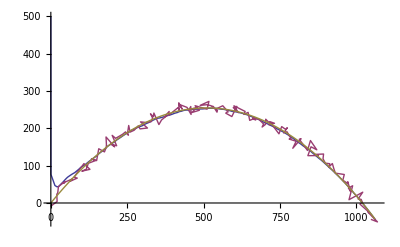

```mathematica
ListLinePlot[{KalmanPoints,NoisyPoints,TruePoints}]
```